```mathematica
ClearAll["Global`*"];
(*ICs - Initial Conditions *)
ffCartPendulum[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,InitGuess_]:=
Module[{x,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	2/(A Cos[2 θ]+A-2)^3 (Cos[θ] (4 Sin[θ] (A λ4^2 Cos[2 θ]+4 A λ2^2+(A+2) λ4^2)-(A Cos[2 θ]-3 A+2) (A Cos[2 θ]+A-2) (A θdot^2 λ2-λ4))+A ((A-2) Cos[2 θ]+A) (A Cos[2 θ]+A-2) (λ2-θdot^2 λ4)-4 λ2 λ4 Sin[θ] (3 A Cos[2 θ]+3 A+2)),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};
Subscript[xGuess, 0]= {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[1]],InitGuess[[1]],InitGuess[[1]]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1]; 
froot=FindRoot[eqns,sv,MaxIterations->maxIter];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,uff0,J}]


CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},

xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Q = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (IdentityMatrix[4] + Afᵀ.S[t] + S[t].Af - KroneckerProduct[S[t].Bf,Bfᵀ.S[t]]) /. {x-> x1a[t], xdot -> xdot1a[t], θ ->θ1a[t], θdot -> θdot1a[t], u -> u1a[t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,S,K},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[t_] := CalculateGains[xff,xdotff,θff,θdotff,uff,t,A,τ,S];
ufb[t_] := Piecewise[{{
K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0<=t<=τ}},κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3(xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0<=t<=τ}},κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3(xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];
J = NIntegrate[us[t]^2,{t,0,τ}];
{xs,xdots,θs,θdots,us,J}]
```

## Improve Feedback

Symbolic Calculations required for obtaining appropriate matrices which will be used to compute the feedback

```mathematica
ClearAll["Global`*"];
Reomve["Global`*"];
xState = {x,xdot,θ,θdot};
λ = {λ1,λ2,λ3,λ4};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
f = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
H = L + λ.f;
Hux = D[Grad[H,xState],u];
Hxx =Grad[Grad[H,xState],xState];
fx = Grad[f,xState];
fu = D[f,u];
At = fx - KroneckerProduct[fu,Hux]; (* Huu = 1*)
Bt = KroneckerProduct[fu,fu];
Ct = Hxx - KroneckerProduct[Hux,Hux];
```

```mathematica
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[t_] := (Ct + Atᵀ.S[t] + S[t].At - S[t].Bt.S[t]) /. {x-> x1a[t], xdot -> xdot1a[t], θ ->θ1a[t], θdot -> θdot1a[t], u -> u1a[t]};
sol2 = S /. NDSolve[{S'[t]== RHS[t],S[0]==S0},S,{t,0,τ }];
S = sol2[[1]]
```

```mathematica
CalculateSMatrix2[x1a_,xdot1a_,θ1a_,θdot1a_,λ1ff_,λ2ff_,λ3ff_,λ4ff_,u1a_,τ_,A_]:= Module[{x,L,RHS1,RHS2,RHS3,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,f,H,Hux,Hxx,fu,fx,At,Bt,Ct,xState,R,Mf,x2dot,θ2dot,S0,sol2,t,λ,λ1,λ2,λ3,λ4,replacement,R0,Q0,eq,init},
xState = {x,xdot,θ,θdot};
λ = {λ1,λ2,λ3,λ4};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));f = {xdot,x2dot,θdot,θ2dot};L = 1/2*u^2;
H = L + λ.f;
Hux = D[Grad[H,xState],u];
Hxx =Grad[Grad[H,xState],xState];
fx = Grad[f,xState];
fu = D[f,u];
At = fx - KroneckerProduct[fu,Hux]; (* Huu = 1*)
Bt = KroneckerProduct[fu,fu];
Ct = Hxx - KroneckerProduct[Hux,Hux];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Q0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
R0 = IdentityMatrix[4];
replacement = {x-> x1a[τ - t], xdot -> xdot1a[τ - t], θ ->θ1a[τ - t], θdot -> θdot1a[τ - t], u -> u1a[τ - t],λ1 -> λ1ff[τ - t],λ2 -> λ2ff[τ - t],λ3 -> λ3ff[τ - t],λ4 -> λ4ff[τ - t]};
RHS1[t_] := (Ct + Atᵀ.S[t] + S[t].At - S[t].Bt.S[t]) /. replacement; (* Note: Eqns are being integrated backwards*)
RHS2[t_] := (Atᵀ.R[t] - S[t].Bt.R[t])/.replacement;
RHS3[t_] := -(R[t]ᵀ.Bt.R[t])/.replacement;
eq = {S'[t] == RHS1[t],R'[t] == RHS2[t],Q'[t] == RHS3[t]};
init = {S[0] == S0,R[0] == R0,Q[0] == Q0};
{S,R,Q} = NDSolveValue[{eq,init},{S,R,Q},{t,0,τ }]
]
```

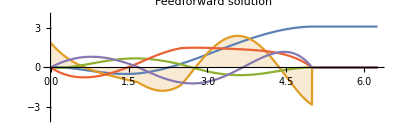

```mathematica
n=6;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;
ICs = {0,0,0,0};
InitGuess = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter,InitGuess]; 
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

```mathematica
{S,R,Q} = CalculateSMatrix2[x1a,xdot1a,θ1a,θdot1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,u1a,τ,A]
```

NDSolveValue::ndsz: At t$341407 == 0.863307, step size is effectively zero; singularity or stiff system suspected.

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
sol
```

{InterpolatingFunction[…]}

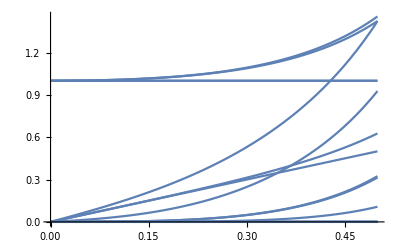

```mathematica
i = 1;j = 2;
Plot[R[t],{t,0,0.5}]
```

## Understanding Effect of Changing n

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$13251 near {t$13251} = {3.25188}. NIntegrate obtained 35.7232 and 0.000165289 for the integral and error estimates.

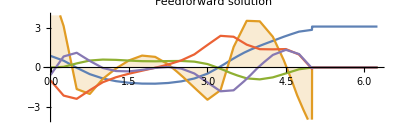

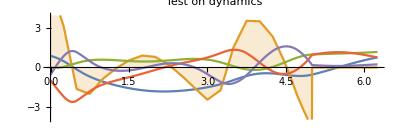

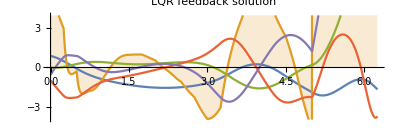

```mathematica
n=20;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100;
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$543645 near {t$543645} = {3.27141}. NIntegrate obtained 62.6641 and 0.000466661 for the integral and error estimates.

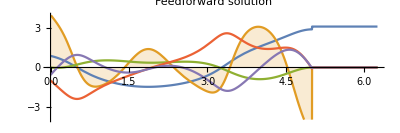

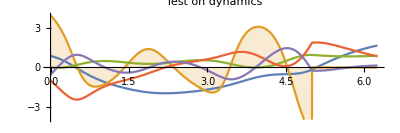

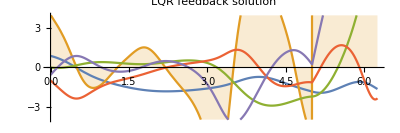

```mathematica
n=234;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100;
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

By Changing n from 234 to 235 we move to a completely new solution!!!

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$584614 near {t$584614} = {3.26164}. NIntegrate obtained 51.5447 and 0.000946889 for the integral and error estimates.

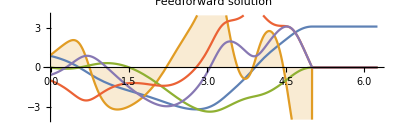

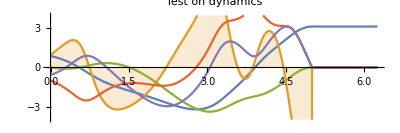

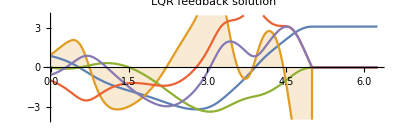

```mathematica
n=235;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 100; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Furthermore reducing the max iterations to 20 also works as the feedback corrects the errors

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 20 iterations.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$591587 near {t$591587} = {2.93938}. NIntegrate obtained 48.7701 and 0.00034475 for the integral and error estimates.

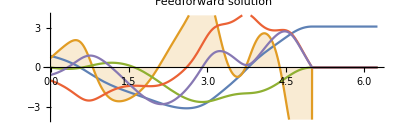

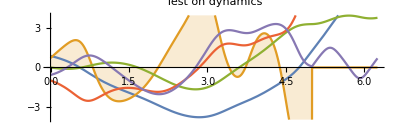

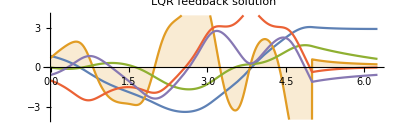

```mathematica
n=235;τ=5;τ1=τ*1.25;A=0.2;order = 1;maxIter = 20; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Can we come up with a better initial guess that would work for smaller values of n

Try this out by down sampling the true optimal values and using them as initial conditions for smaller values of n

Standard Case

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 40 iterations.

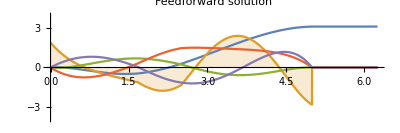

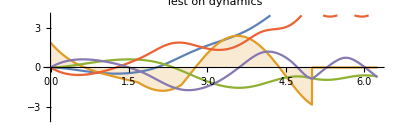

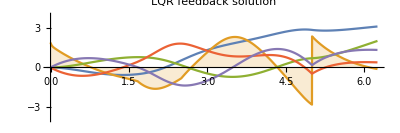

```mathematica
n=6;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 40; (* Order of Interpolation doesnt matter for such large n*)
xdotMin = -1;
xdotMax = 1;
θMin = -π;
θMax = π;
θdotMin = -1;
θdotMax = 1;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit}; (* Random Initialization *)
ICs={0.89486028245609,-0.9468360111172656,-0.002994757534002989,1.677668990900959}; (* Works *)
ICs = {0,-0.5735358669582524,0.8898706763193971,-0.9946572285334812}; (* Doesnt Work *)
ICs = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A,order,maxIter]; 
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"LQR feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```